# Nanobot Theory : Data Analysis and Plotting

#### Yibin Jiang, Abhishek Sharma Cronin Lab University of Glasgow

```mathematica
ClearAll[deviationslLLP]
deviationslLLP[ave_,dev_,opts:OptionsPattern[]]:=Module[{
fill=Join@@(Thread[Range[Length@ave]->List/@(Length[ave] #+Range[Length@ave])]&/@{1,2}),
apd=Style[#,Opacity[0]]&/@(ave+dev),
amd=Style[#,Opacity[0]]&/@(ave-dev),p1,p2},
p1=ListLinePlot[Join@@{ave,apd,amd},Filling->fill,opts]
]
```

```mathematica
initialDipole = Import[NotebookDirectory[]<>"/data/initial_dipoles.csv"];
finalDipole = Import[NotebookDirectory[]<>"/data/final_structure_5.csv"];
Print[Length[initialDipole]];
Print[Length[finalDipole]];
```

1329

4089

```mathematica
4089-1329
```

2760

```mathematica
d=0.41*10^-3;
```

```mathematica
maxposition = Table[Flatten@Import[NotebookDirectory[]<>ToString[repeat]<>"/max_peak_wv.csv"],{repeat,0,9}];
minposition = Table[Flatten@Import[NotebookDirectory[]<>ToString[repeat]<>"/smaller_peak_wv.csv"],{repeat,0,9}];
maxcross = Table[Flatten@Import[NotebookDirectory[]<>ToString[repeat]<>"/max_peak_cross.csv"],{repeat,0,9}];
mincross =  Table[Flatten@Import[NotebookDirectory[]<>ToString[repeat]<>"/smaller_peak_cross.csv"],{repeat,0,9}];
```

```mathematica
Qmaxcross=Table[
reffi = (3/(4π)d^3*(1328+step) )^(1/3);
maxcross⟦repeat⟧⟦step⟧/(π reffi^2),{repeat,10},{step,2761}];
```

```mathematica
Qmincross=Table[
reffi = (3/(4π)d^3*(1328+step) )^(1/3);
mincross⟦repeat⟧⟦step⟧/(π reffi^2),{repeat,10},{step,2761}];
```

```mathematica
intermediates=Flatten@{0,408,420,416,396,360,308,240,156,56}
```

{0,408,420,416,396,360,308,240,156,56}

```mathematica
position =Table[Total[intermediates⟦1;;i⟧],{i,Length[intermediates]}];
lineStyle={Thick,Black,Dashed};
lines = Table[Line[{{position⟦i⟧,0},{position⟦i⟧,1000}}],{i,Length[position]}];
```

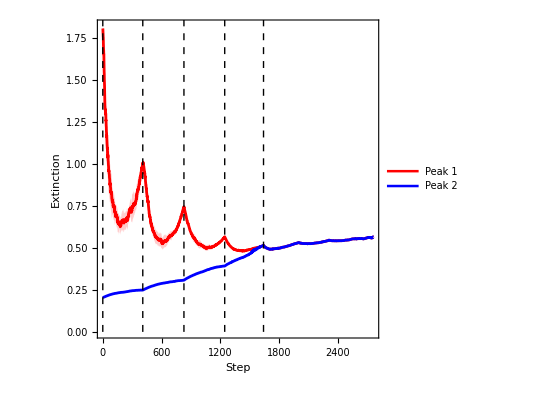

```mathematica
f1 = deviationslLLP[
{Mean[Qmaxcross],Mean[Qmincross]},{StandardDeviation[Qmaxcross]+0.0000000000001,StandardDeviation[Qmincross]+0.0000000000001},
DataRange->{0,Length[Mean[Qmaxcross]] - 1},
PlotStyle->{{Red,Thickness[0.005]},{Blue,Thickness[0.005]}},AspectRatio->1,PlotLegends->Placed[{"Peak 1","Peak 2"},{0.8,0.8}],LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->18]},FrameLabel->{"Step","Extinction"},PlotRange->All,Frame->True,FrameStyle->{{Thick,Thick},{Thick,Thick}},FrameTicksStyle->{{Thick,Thick},{Thick,Thick}},ImageSize->400,Epilog->{{Directive[lineStyle],lines⟦1;;5⟧},{Directive[Thick,Black]}}]
Export[NotebookDirectory[]<>"Extinction.png",f1,ImageResolution->300];
```

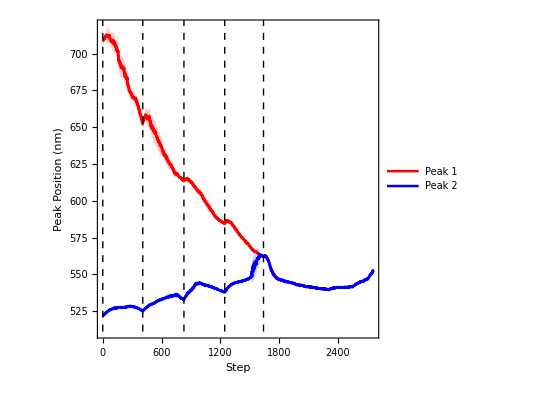

```mathematica
f1 = deviationslLLP[
1000*{Mean[maxposition],Mean[minposition]},1000*{StandardDeviation[maxposition]+0.0000000000001,StandardDeviation[minposition]+0.0000000000001},
DataRange->{0,Length[Mean[maxposition]] - 1},PlotStyle->{{Red,Thickness[0.005]},{Blue,Thickness[0.005]}},AspectRatio->1,PlotLegends->Placed[{"Peak 1","Peak 2"},{0.8,0.8}],LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->18]},FrameLabel->{"Step","Peak Position (nm)"},Frame->True,FrameStyle->{{Thick,Thick},{Thick,Thick}},FrameTicksStyle->{{Thick,Thick},{Thick,Thick}},ImageSize->400,Epilog->{{Directive[lineStyle],lines⟦1;;5⟧},{Directive[Thick,Black]}}]
Export[NotebookDirectory[]<>"Peak_Position.png",f1,ImageResolution->300];
```